## Линейный конгруэнтный генератор

```mathematica
nMax=1024;
mod = 2^10;
(*lc[m_,a_,c_,x_]:=,*)
lkp[m_,a_,c_,x_]:=RecurrenceTable[
{X[n+1]==Mod[(a*X[n]+c),m],X[1]==x},
X,
{n,1,nMax}
];
t = Table[{ListPlot[lkp[mod,a,c,0]], a,c}, {a,27,47,1},{c,1,20,3}];
```

```mathematica
m =NextPrime[1024]
```

1031

```mathematica
Mod[(0*430+2531),1024]
```

483

```mathematica
Mod[lkp[1031,430,101, 0] , 1024]
```

{0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489,47,722,230,25,541,756,416,618,874,637,796,89,224,538,497,394,437,369,4,873,207,445,716,743,1012,179,777,167,772,79,48,121,581,429,22,282,734,235,113,234,714,914,310,402,784,84,136,845,539,927,745,841,881,554,160,855,715,313,661,806,265,641,454,462,809,524,663,635,967,418,447,545,414,789,172,860,803,6,619,273,988,169,601,781,856,114,664,34,287,822,959,71,732,406,442,457,721,831,705,137,244,890,300,226,367,168,171,430,452,633,107,747,670,552,331,153,938,320,578,170,0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489,47,722,230,25,541,756,416,618,874,637,796,89,224,538,497,394,437,369,4,873,207,445,716,743,1012,179,777,167,772,79,48,121,581,429,22,282,734,235,113,234,714,914,310,402,784,84,136,845,539,927,745,841,881,554,160,855,715,313,661,806,265,641,454,462,809,524,663,635,967,418,447,545,414,789,172,860,803,6,619,273,988,169,601,781,856,114,664,34,287,822,959,71,732,406,442,457,721,831,705,137,244,890,300,226,367,168,171,430,452,633,107,747,670,552,331,153,938,320,578,170,0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489,47,722,230,25,541,756,416,618,874,637,796,89,224,538,497,394,437,369,4,873,207,445,716,743,1012,179,777,167,772,79,48,121,581,429,22,282,734,235,113,234,714,914,310,402,784,84,136,845,539,927,745,841,881,554,160,855,715,313,661,806,265,641,454,462,809,524,663,635,967,418,447,545,414,789,172,860,803,6,619,273,988,169,601,781,856,114,664,34,287,822,959,71,732,406,442,457,721,831,705,137,244,890,300,226,367,168,171,430,452,633,107,747,670,552,331,153,938,320,578,170,0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489,47,722,230,25,541,756,416,618,874,637,796,89,224,538,497,394,437,369,4,873,207,445,716,743,1012,179,777,167,772,79,48,121,581,429,22,282,734,235,113,234,714,914,310,402,784,84,136,845,539,927,745,841,881,554,160,855,715,313,661,806,265,641,454,462,809,524,663,635,967,418,447,545,414,789,172,860,803,6,619,273,988,169,601,781,856,114,664,34,287,822,959,71,732,406,442,457,721,831,705,137,244,890,300,226,367,168,171,430,452,633,107,747,670,552,331,153,938,320,578,170,0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489,47,722,230,25,541,756,416,618,874,637,796,89,224,538,497,394,437,369,4,873,207,445,716,743,1012,179,777,167,772,79,48,121,581,429,22,282,734,235,113,234,714,914,310,402,784,84,136,845,539,927,745,841,881,554,160,855,715,313,661,806,265,641,454,462,809,524,663,635,967,418,447,545,414,789,172,860,803,6,619,273,988,169,601,781,856,114,664,34,287,822,959,71,732,406,442,457,721,831,705,137,244,890,300,226,367,168,171,430,452,633,107,747,670,552,331,153,938,320,578,170,0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489,47,722,230,25,541,756,416,618,874,637,796,89,224,538,497,394,437,369,4,873,207,445,716,743,1012,179,777,167,772,79,48,121,581,429,22,282,734,235,113,234,714,914,310,402,784,84,136,845,539,927,745,841,881,554,160,855,715,313,661,806,265,641,454,462,809,524,663,635,967,418,447,545,414,789,172,860,803,6,619,273,988,169,601,781,856,114,664,34,287,822,959,71,732,406,442,457,721,831,705,137,244,890,300,226,367,168,171,430,452,633,107,747,670,552,331,153,938,320,578,170,0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489,47,722,230,25,541,756,416,618,874,637,796,89,224,538,497,394,437,369,4,873,207,445,716,743,1012,179,777,167,772,79,48,121,581,429,22,282,734,235,113,234,714,914,310,402,784,84,136,845,539,927,745,841,881,554,160,855,715,313,661,806,265,641,454,462,809,524,663,635,967,418,447,545,414,789,172,860,803,6,619,273,988,169,601,781,856,114,664,34,287,822,959,71,732,406,442,457,721,831,705,137,244,890,300,226,367,168,171,430,452,633,107,747,670,552,331,153,938,320,578,170,0,101,229,626,190,352,935,61,556,1020,526,492,306,744,411,530,150,679,298,397,696,391,178,347,847,368,598,522,834,964,159,425,364,940,149,249,978,0,184,865,891,730,577,771,680,728,748,69,903,735,665,464,638,195,440,628,19,23,712,54,639,625,791,1,531,580,6,702,909,222,709,826,617,444,286,392,608,698,220,880,124,840,451,203,787,343,158,2,13,536,668,723,660,376,945,237,973,936,491,907,393,7,18,624,361,681,127,68,473,384,261,983,81,908,823,358,422,105,918,999,775,338,70,302,55,38,976,164,513,57,898,647,972,506,140,503,912,481,731,1007,91,53,209,274,387,520,1005,262,382,432,281,304,915,740,753,157,596,693,132,156,166,342,759,675,640,24,111,405,12,106,317,319,148,850,627,620,703,308,573,82,307,143,762,934,662,205,616,14,966,1019,96,141,933,232,885,212,533,409,701,479,902,305,314,60,126,669,122,1011,780,426,794,260,553,761,504,311,832,104,488,648,371,857,544,1015,438,799,348,246,719,1002,3,360,251,807,695,992,858,974,335,842,280,905,564,336,241,631,278,45,893,559,248,548,673,811,353,334,412,960,501,52,810,954,1014,8,448,975,765,162,684,386,90,654,889,901,906,994,687,645,112,835,363,510,829,876,466,467,897,217,621,102,659,977,594,864,461,379,173,259,123,410,100,830,275,817,871,378,774,939,750,929,574,512,658,547,243,460,980,853,886,642,884,813,182,5,189,953,584,688,44,463,208,875,36,116,493,736,64,815,11,707,997,946,667,293,309,1003,433,711,655,288,221,279,475,213,963,760,74,991,428,623,962,330,754,587,947,66,644,713,484,990,5,272,558,849,197,269,299,827,16,795,690,904,134,1016,868,119,752,758,245,289,651,630,879,725,489}

### Графики последовательностей с разными начальным значением

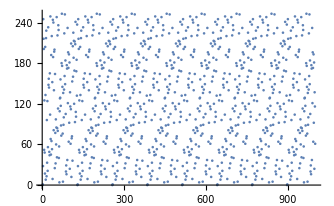
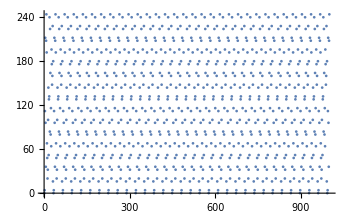
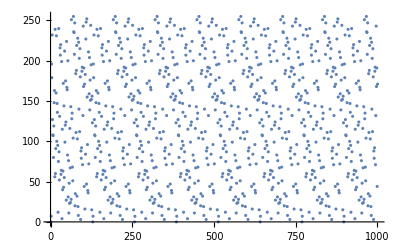
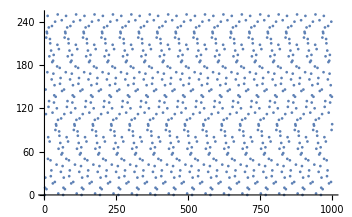
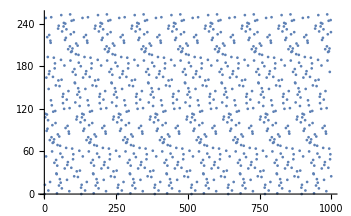
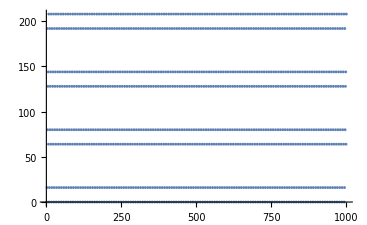
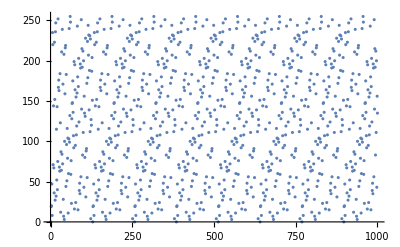
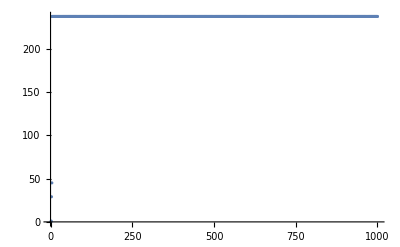
{{{-Graphics-,27,1},{-Graphics-,27,4},{-Graphics-,27,7},{-Graphics-,27,10},{-Graphics-,27,13},{-Graphics-,27,16},{-Graphics-,27,19}},{{-Graphics-,28,1},{-Graphics-,28,4},{-Graphics-,28,7},{-Graphics-,28,10},{-Graphics-,28,13},{-Graphics-,28,16},{-Graphics-,28,19}},{{-Graphics-,29,1},{-Graphics-,29,4},{-Graphics-,29,7},{-Graphics-,29,10},{-Graphics-,29,13},{-Graphics-,29,16},{-Graphics-,29,19}},{{-Graphics-,30,1},{-Graphics-,30,4},{-Graphics-,30,7},{-Graphics-,30,10},{-Graphics-,30,13},{-Graphics-,30,16},{-Graphics-,30,19}},{{-Graphics-,31,1},{-Graphics-,31,4},{-Graphics-,31,7},{-Graphics-,31,10},{-Graphics-,31,13},{-Graphics-,31,16},{-Graphics-,31,19}},{{-Graphics-,32,1},{-Graphics-,32,4},{-Graphics-,32,7},{-Graphics-,32,10},{-Graphics-,32,13},{-Graphics-,32,16},{-Graphics-,32,19}},{{-Graphics-,33,1},{-Graphics-,33,4},{-Graphics-,33,7},{-Graphics-,33,10},{-Graphics-,33,13},{-Graphics-,33,16},{-Graphics-,33,19}},{{-Graphics-,34,1},{-Graphics-,34,4},{-Graphics-,34,7},{-Graphics-,34,10},{-Graphics-,34,13},{-Graphics-,34,16},{-Graphics-,34,19}},{{-Graphics-,35,1},{-Graphics-,35,4},{-Graphics-,35,7},{-Graphics-,35,10},{-Graphics-,35,13},{-Graphics-,35,16},{-Graphics-,35,19}},{{-Graphics-,36,1},{-Graphics-,36,4},{-Graphics-,36,7},{-Graphics-,36,10},{-Graphics-,36,13},{-Graphics-,36,16},{-Graphics-,36,19}},{{-Graphics-,37,1},{-Graphics-,37,4},{-Graphics-,37,7},{-Graphics-,37,10},{-Graphics-,37,13},{-Graphics-,37,16},{-Graphics-,37,19}},{{-Graphics-,38,1},{-Graphics-,38,4},{-Graphics-,38,7},{-Graphics-,38,10},{-Graphics-,38,13},{-Graphics-,38,16},{-Graphics-,38,19}},{{-Graphics-,39,1},{-Graphics-,39,4},{-Graphics-,39,7},{-Graphics-,39,10},{-Graphics-,39,13},{-Graphics-,39,16},{-Graphics-,39,19}},{{-Graphics-,40,1},{-Graphics-,40,4},{-Graphics-,40,7},{-Graphics-,40,10},{-Graphics-,40,13},{-Graphics-,40,16},{-Graphics-,40,19}},{{-Graphics-,41,1},{-Graphics-,41,4},{-Graphics-,41,7},{-Graphics-,41,10},{-Graphics-,41,13},{-Graphics-,41,16},{-Graphics-,41,19}},{{-Graphics-,42,1},{-Graphics-,42,4},{-Graphics-,42,7},{-Graphics-,42,10},{-Graphics-,42,13},{-Graphics-,42,16},{-Graphics-,42,19}},{{-Graphics-,43,1},{-Graphics-,43,4},{-Graphics-,43,7},{-Graphics-,43,10},{-Graphics-,43,13},{-Graphics-,43,16},{-Graphics-,43,19}},{{-Graphics-,44,1},{-Graphics-,44,4},{-Graphics-,44,7},{-Graphics-,44,10},{-Graphics-,44,13},{-Graphics-,44,16},{-Graphics-,44,19}},{{-Graphics-,45,1},{-Graphics-,45,4},{-Graphics-,45,7},{-Graphics-,45,10},{-Graphics-,45,13},{-Graphics-,45,16},{-Graphics-,45,19}},{{-Graphics-,46,1},{-Graphics-,46,4},{-Graphics-,46,7},{-Graphics-,46,10},{-Graphics-,46,13},{-Graphics-,46,16},{-Graphics-,46,19}},{{-Graphics-,47,1},{-Graphics-,47,4},{-Graphics-,47,7},{-Graphics-,47,10},{-Graphics-,47,13},{-Graphics-,47,16},{-Graphics-,47,19}}}

```mathematica
t
```